If you find this useful, please cite Kesava, Sameer Vajjala; Department of Physics, University of Oxford.

```mathematica
SetDirectory["/home/sameer/Dropbox/Oxford Projects/Link to Documents/Work with Ivan"] (*Set the working directory*)
```

/home/sameer/Dropbox/Oxford Projects/Link to Documents/Work with Ivan

```mathematica
Data = Import["TAPC5pc12hrsUVdim.xlsx", {"Data",1}]; (*Import Transmittance data from excel*)
```

```mathematica
Data[[1]] (*Should be of the format {wavelength in nm, Transmittance}*)
```

{210.,0.85457}

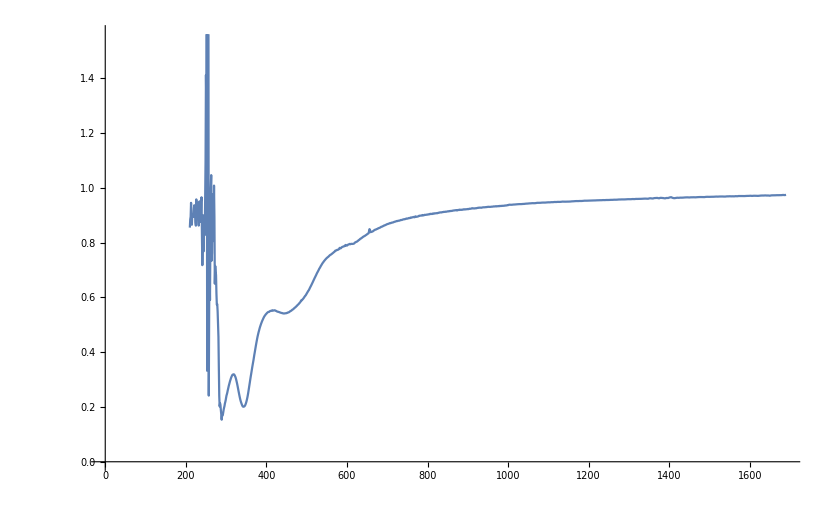

```mathematica
ListLinePlot[Data]
```

```mathematica
Data2 = Drop[Data, 70]; (*Filtering out unphysical data points by choosing a reasonable starting point*)
Data2[[1]]
```

{280.,0.50162}

```mathematica
TrData =Transpose[Data2];
```

#### Constants

```mathematica
thickness = 50 (* thickness of the film in nm*);
h = 6.626*10^(-34);
c = 3*10^(8);
q = 1.602*10^(-19);
```

#### Converting data into extinction coefficient

```mathematica
TrData⟦2⟧=-(Log[TrData⟦2⟧] TrData⟦1⟧)/(thickness (4 π)); (*Converting Transmittance into k*)
```

```mathematica
TrData[[1]] = (c*h)/(q*TrData[[1]]*10^(-9)); (*Converting nm into eV*)
```

```mathematica
FinalData = Sort[Transpose[TrData], #1[[1]]<#2[[1]]&];
```

#### Plotting extinction coefficient derived from Transmittance/Absorbance data

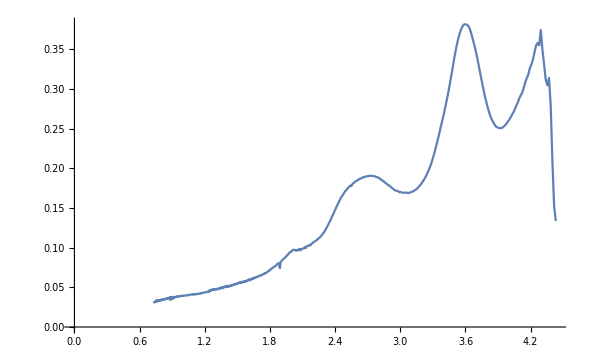

```mathematica
ListLinePlot[FinalData]
```

```mathematica
Plotdata=FinalData;
```

```mathematica
Plotdata[[1]]
```

{0.734215,0.0307012}

```mathematica
Plotdata[[1,2]]
```

0.0307012

## Using a combination (will vary with material) of Lorentz and TaucLorentz functions to fit to the k data

```mathematica
Lorentz[x_,k_,ω0_,Γ_]:=(Γ k x)/(Γ^2 x^2+(ω0^2-x^2)^2);
```

```mathematica
TaucLorentz[x_,k_,ω0_,Γ_,Eg_]:=(ω0 Γ k (x-Eg)^2)/((Γ^2 x^2+(x^2-ω0^2)^2) x);
```

```mathematica
fit1 = NonlinearModelFit[Plotdata,{TaucLorentz[x, k1,ω01,Γ1, ωg1] + Lorentz[x, k2,ω02,Γ2]+Lorentz[x, k3,ω03,Γ3] +TaucLorentz[x, k4,ω04,Γ4,ωg4]+Lorentz[x, k5,ω05,Γ5], ω01>0,k1>0, ωg1>0, ω02>0, k2>0,ω03>0,k3>0, ω04>0, k4>0,ωg4>0,ω05>0, k5>0}, {{k1,0.001},{ω01,4.3},{Γ1, 0.414},{ωg1,0.8}, { k2,0.3},{ω02,2.7} ,{Γ2,1},(*{ωg2,2},*){k3,0.6},{ω03,3.6},{Γ3,0.5},(* {ωg3,3},*){k4,0.15}, {ω04,2.24},{Γ4,2},{ωg4,1},{k5,0.15},{ω05,2},{Γ5, 1.5}},x, MaxIterations->100000]
```

FittedModel[(0.907802 x)/(16.2039 x^2+(4.86949-x^2)^2)+(0.289604 x)/(0.757236 x^2+(«18»-«1»)^2)+(«1»)/(«1»)+(0.221627 «1»)/(x («20» x^2+(«1»)^2))+(0.00237683 (-0.00194378+x)^2)/(x (0.0771119 x^2+(-3.91856+x^2)^2))]

```mathematica
fit1["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
k1 | 0.122877 | 0.110003 | 1.11704 | 0.264251
ω01 | 4.25303 | 0.00640012 | 664.523 | 3.76510695709×10^-1303
Γ1 | 0.424084 | 0.00841291 | 50.4087 | 2.03624×10^-274
ωg1 | 0.000290293 | 1.92357 | 0.000150913 | 0.99988
k2 | 0.332805 | 0.0409693 | 8.12327 | 1.35743×10^-15
ω02 | 2.7057 | 0.00451623 | 599.105 | 3.75279123996×10^-1259
Γ2 | 0.870193 | 0.0462107 | 18.831 | 9.34322×10^-68
k3 | 0.619319 | 0.0222661 | 27.8144 | 5.66508×10^-126
ω03 | 3.61177 | 0.00184445 | 1958.18 | 1.08780630153×10^-1762
Γ3 | 0.548 | 0.00998807 | 54.8654 | 4.78351×10^-301
k4 | 0.00432389 | 0.0154907 | 0.279128 | 0.780205
ω04 | 1.97954 | 0.0261206 | 75.7844 | 4.23064028764×10^-412
Γ4 | 0.27769 | 0.048017 | 5.78317 | 9.8518×10^-9
ωg4 | 0.00194378 | 3.65513 | 0.000531795 | 0.999576
k5 | 0.225518 | 0.232617 | 0.969482 | 0.332544
ω05 | 2.20669 | 0.848408 | 2.60098 | 0.00943584
Γ5 | 4.02541 | 2.59078 | 1.55375 | 0.120568

```mathematica
fit1["BestFitParameters"]
```

{k1→0.122877,ω01→4.25303,Γ1→0.424084,ωg1→0.000290293,k2→0.332805,ω02→2.7057,Γ2→0.870193,k3→0.619319,ω03→3.61177,Γ3→0.548,k4→0.00432389,ω04→1.97954,Γ4→0.27769,ωg4→0.00194378,k5→0.225518,ω05→2.20669,Γ5→4.02541}

```mathematica
fit1["RSquared"]
```

0.998503

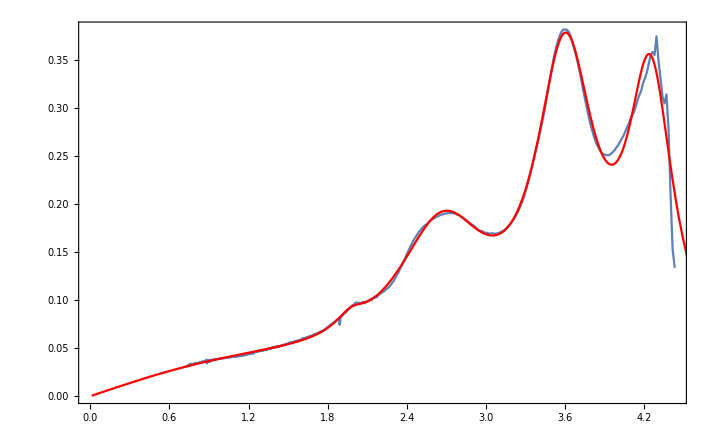

```mathematica
Plot1 = Show[ListLinePlot[Plotdata], Plot[fit1[x], {x, 0.01,20}, PlotStyle->Red, PlotRange->All], Frame->True ]
```

```mathematica
K1 = k1/.fit1["BestFitParameters"];
W1 = ω01/.fit1["BestFitParameters"];
T1 = Γ1/.fit1["BestFitParameters"];
Wg1 = ωg1/.fit1["BestFitParameters"];
K2 = k2/.fit1["BestFitParameters"];
W2 = ω02/.fit1["BestFitParameters"];
T2 = Γ2/.fit1["BestFitParameters"];
K3 = k3/.fit1["BestFitParameters"];
W3= ω03/.fit1["BestFitParameters"];
T3= Γ3/.fit1["BestFitParameters"];
K4 = k4/.fit1["BestFitParameters"];
W4= ω04/.fit1["BestFitParameters"];
T4= Γ4/.fit1["BestFitParameters"];
Wg4 = ωg4/.fit1["BestFitParameters"];
K5 = k5/.fit1["BestFitParameters"];
W5 = ω05/.fit1["BestFitParameters"];
T5 = Γ5/.fit1["BestFitParameters"];
```

Copy the parameter values into a set of constants

## Equation for Dispersion n derived from Kramers-Kronig equation

### n for TaucLorentz

```mathematica
α[ω0_,Γ_]:=√(4 ω0^2-Γ^2);
γ[ω0_,Γ_]:=√(ω0^2-Γ^2/2);
ζ[x_,ω0_,Γ_]:=(x^2-γ[ω0,Γ]^2)^2+1/4 α[ω0,Γ]^2 Γ^2;
```

```mathematica
nTaucLorentz[x_,k_,ω0_,Γ_,ωg_]:=(k Γ ((ωg^2-ω0^2) x^2+ωg^2 Γ^2-ω0^2 (ω0^2+3 ωg^2)) Log[(ω0^2+ωg^2+α[ω0,Γ] ωg)/(ω0^2+ωg^2-α[ω0,Γ] ωg)])/(π ζ[x,ω0,Γ] 2 α[ω0,Γ] ω0)-(k ((x^2-ω0^2) (ω0^2+ωg^2)+ωg^2 Γ^2) (π-ArcTan[(2 ωg+α[ω0,Γ])/Γ]+ArcTan[(-2 ωg+α[ω0,Γ])/Γ]))/(π ζ[x,ω0,Γ] ω0)+(2 k ω0 ωg (x^2-γ[ω0,Γ]^2) (π+2 ArcTan[(2 (γ[ω0,Γ]^2-ωg^2))/(α[ω0,Γ] Γ)]))/(π ζ[x,ω0,Γ] α[ω0,Γ])-(k ω0 Γ (x^2+ωg^2) Log[Abs[x-ωg]/(x+ωg)])/(π ζ[x,ω0,Γ] x)+(2 k ω0 Γ ωg Log[(Abs[x-ωg] (x+ωg))/(√((ω0^2+ωg^2)^2+ωg^2 Γ^2))])/(π ζ[x,ω0,Γ]);
```

### n for Lorentz

```mathematica
nLorentz[x_,k_,ω0_,Γ_]:=(k (ω0^2-x^2))/((x^2-ω0^2)^2+Γ^2 x^2);
```

### Final equation for n using the above fitted functions

```mathematica
n∞ = 2;
```

Have to add n∞ manually, choosing a value of 2 for organic semiconductors

```mathematica
Finaln[x_]:=n∞+nTaucLorentz[x, K1,W1,T1,Wg1] + nLorentz[x, K2,W2,T2]+nLorentz[x, K3,W3, T3] +nTaucLorentz[x, K4, W4, T4,Wg4]+nLorentz[x, K5,W5,T5];
```

Use the above combination of functions to obtain n

### Plotting n without n∞

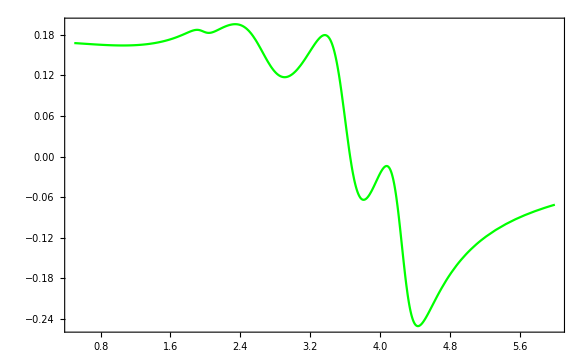

```mathematica
Plot[Finaln[x]- n∞, {x, 0.5,6}, Frame-> True, PlotRange-> All, PlotStyle->Green]
```

### Plotting n with n∞

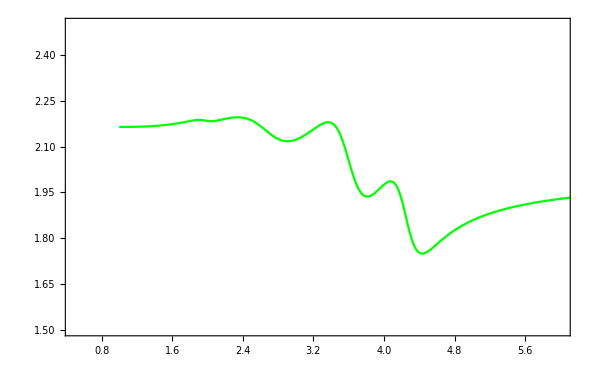

```mathematica
Plot2=Plot[Finaln[x], {x, 1,8}, Frame-> True, PlotRange-> {{0.5,6},{1.5,2.5}}, PlotStyle->Green]
```

## Plotting All

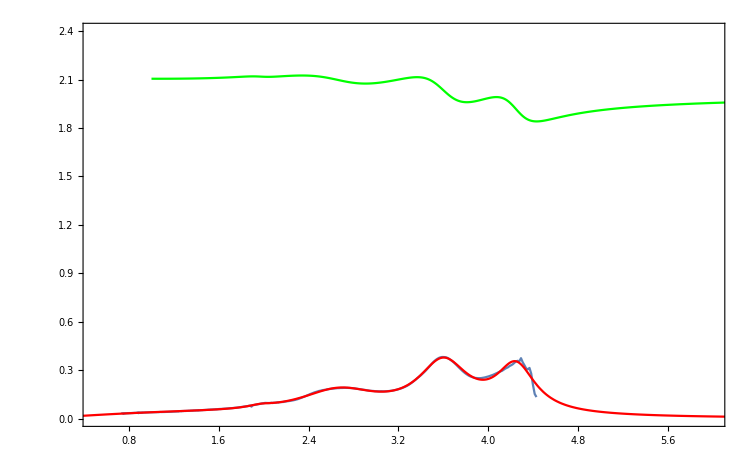

```mathematica
Show[Plot1,Plot2, PlotRange->{{0.5,6},{0,2.4}}]
```

## Exporting Data

```mathematica
Exportdata = Table[{h*c/(q*Plotdata[[i,1]]*10^(-9)),Finaln[Plotdata[[i,1]]],fit2[Plotdata[[i,1]]], Plotdata[[i,2]]},{i,1,Length[Plotdata]}];
```

```mathematica
Export["Refractive_Index.xlsx",Join[{{"Wavelength (nm)", "n_KK", "k_fit", "k_data"}},Exportdata]];
```